```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=320; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
snu=(snu1+snu2)/1.5;
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
(*slice=snu*n/(bin/2);
xevent=ConstantArray[0,bin+1];
pevent=ConstantArray[0,bin+1];
(*63*)
(*X-Quadrature of the Data*)
xsize=Dimensions[allData[[6]][[19;;]]];
xsize=xsize[[1]];
xquad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,xsize}];

(*P-Quadrature of the Data*)
psize=Dimensions[allData[[3]][[19;;]]];
psize=psize[[1]];
pquad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,psize}];*)
```

## (+) Cat state theoretical generation

```mathematica
slice=snu*n/(bin/2);
(*hbar=1*)
x0=2;
plusx[x_]=Exp[(-(x-x0)^2)/2]+Exp[(-(x+x0)^2)/2];
plusp[x_]=Exp[-(x^2)/2]*Cos[x0*x];
```

## Cat State Event

```mathematica
xevent=Table[(plusx[(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
xnorm=Sum[xevent[[i]],{i,1,bin+1}];
xnorm//N
xevent=xevent/xnorm;
Sum[xevent[[i]],{i,1,bin+1}]//N
pevent=Table[(plusp[(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
pnorm=Sum[pevent[[i]],{i,1,bin+1}];
pnorm//N
pevent=pevent/pnorm;
Sum[pevent[[i]],{i,1,bin+1}]//N
```

72.1967

1.

18.0492

1.

## Counting Events

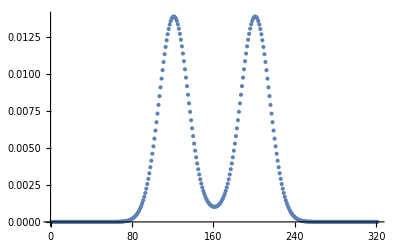

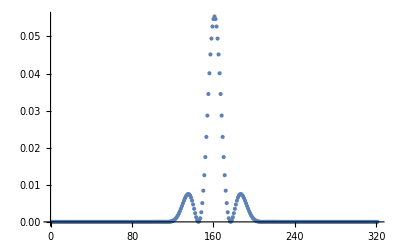

```mathematica
(*(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
xevent=xevent/xsize;
pevent=pevent/psize;*)

(*Gmn is imported, discretized and normalized occurence of event*)
G={xevent,pevent}//N;
ListPlot[xevent, PlotRange->Full]
ListPlot[pevent,PlotRange->Full]
```

## Normalization Parameter for Projector

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
```

20.

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/2};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,2}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
solution=FindMinimum[Q,kernel];

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(0.269068 | -0.000268256+0.00111726 ⅈ | 0.373683+0.00325143 ⅈ | 0.000341698-0.00181138 ⅈ | 0.21923+0.00301314 ⅈ | -0.000139883-0.0000602036 ⅈ | 0.0795513-0.00398448 ⅈ | -0.0000139679+0.00130397 ⅈ | 0.0226507-0.0102036 ⅈ
-0.000268256-0.00111726 ⅈ | 0.000069543 | -0.000395955-0.00159369 ⅈ | 0.0000129712+4.41544×10^-7 ⅈ | -0.000357272-0.00102482 ⅈ | -3.8321×10^-7+3.94053×10^-7 ⅈ | -0.0000144738-0.00023664 ⅈ | 6.08193×10^-6-1.10871×10^-6 ⅈ | -0.0000768717-0.000110015 ⅈ
0.373683-0.00325143 ⅈ | -0.000395955+0.00159369 ⅈ | 0.520347 | 0.000418972-0.00251816 ⅈ | 0.305201+0.00179737 ⅈ | -0.000191846-0.0000894238 ⅈ | 0.10863-0.00608797 ⅈ | -0.0000134632+0.00177447 ⅈ | 0.0307748-0.0140633 ⅈ
0.000341698+0.00181138 ⅈ | 0.0000129712-4.41544×10^-7 ⅈ | 0.000418972+0.00251816 ⅈ | 0.0000280646 | 0.000198476+0.00143541 ⅈ | -2.78051×10^-7-2.37498×10^-7 ⅈ | 0.000172709+0.00054567 ⅈ | -9.32013×10^-6+4.59396×10^-6 ⅈ | 0.000158205+0.000137464 ⅈ
0.21923-0.00301314 ⅈ | -0.000357272+0.00102482 ⅈ | 0.305201-0.00179737 ⅈ | 0.000198476-0.00143541 ⅈ | 0.17981 | -0.00011234-0.0000549232 ⅈ | 0.0638705-0.00370546 ⅈ | -4.51635×10^-6+0.00103531 ⅈ | 0.0178994-0.00830593 ⅈ
-0.000139883+0.0000602036 ⅈ | -3.8321×10^-7-3.94053×10^-7 ⅈ | -0.000191846+0.0000894238 ⅈ | -2.78051×10^-7+2.37498×10^-7 ⅈ | -0.00011234+0.0000549232 ⅈ | 4.72954×10^-7 | -0.000043327+0.0000120976 ⅈ | 7.29436×10^-7-8.40709×10^-7 ⅈ | -0.0000150073-8.90744×10^-6 ⅈ
0.0795513+0.00398448 ⅈ | -0.0000144738+0.00023664 ⅈ | 0.10863+0.00608797 ⅈ | 0.000172709-0.00054567 ⅈ | 0.0638705+0.00370546 ⅈ | -0.000043327-0.0000120976 ⅈ | 0.0263977 | -4.41246×10^-6+0.000434805 ⅈ | 0.00755796-0.00339688 ⅈ
-0.0000139679-0.00130397 ⅈ | 6.08193×10^-6+1.10871×10^-6 ⅈ | -0.0000134632-0.00177447 ⅈ | -9.32013×10^-6-4.59396×10^-6 ⅈ | -4.51635×10^-6-0.00103531 ⅈ | 7.29436×10^-7+8.40709×10^-7 ⅈ | -4.41246×10^-6-0.000434805 ⅈ | 0.0000105362 | -0.000071319-0.000196333 ⅈ
0.0226507+0.0102036 ⅈ | -0.0000768717+0.000110015 ⅈ | 0.0307748+0.0140633 ⅈ | 0.000158205-0.000137464 ⅈ | 0.0178994+0.00830593 ⅈ | -0.0000150073+8.90744×10^-6 ⅈ | 0.00755796+0.00339688 ⅈ | -0.000071319+0.000196333 ⅈ | 0.0042694)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=4;
xrange={-5,5};
yrange={-5,5};
linespace=100;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
disp=Sqrt[((50-pos[[1,1]])/10)^2+((50-pos[[1,2]])/10)^2]//N
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False,DataRange->{{-5,5},{-5,5}}]
```

{{51,51}}

0.141421

-Graphics3D-